```mathematica
S=NDSolve[{D[U[x,t],t]==1/2D[U[x,t],{x,2}]+((x+1)*Sin[x]),U[0,t]==0.5*(0.5+t),U[1,t]==2.25,U[x,0]==(x+0.5)^2},U,{x,0,1},{t,0,0.1}]
```

{{U→InterpolatingFunction[…]}}

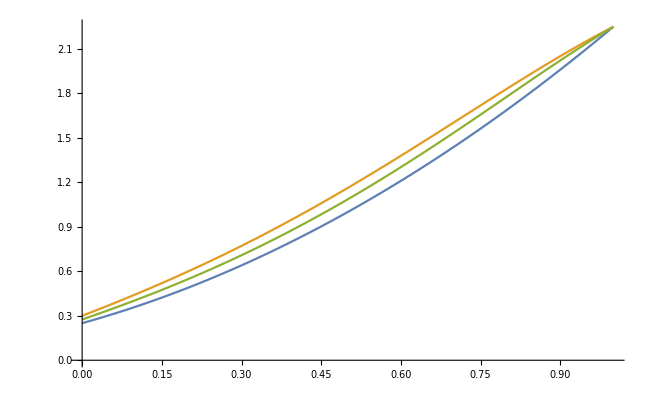

```mathematica
Plot[{Evaluate[U[x,0]/.S],Evaluate[U[x,0.1]/.S],Evaluate[U[x,0.05]/.S]},{x,0,1}]
```